```mathematica
SetDirectory[NotebookDirectory[]];
```

## Setup coordinate frames

```mathematica
xhat = {1, 0, 0}
yhat = {0, 1, 0}
zhat = {0, 0 ,1}
```

{1,0,0}

{0,1,0}

{0,0,1}

```mathematica
θzrot[t_] := RotationMatrix[θ[t], zhat]
ϕxrot[t_] := RotationMatrix[ϕ[t], xhat]

rhat[t_] := ϕxrot[t].θzrot[t].yhat
θhat[t_] := ϕxrot[t].θzrot[t].xhat
ϕhat[t_] := ϕxrot[t].θzrot[t].zhat

rvec[t_] := r rhat[t]
svec[t_]:=x[t] xhat+ z[t] zhat;
hvec[t_]:=svec[t]+rvec[t]
```

```mathematica
(*rhat'[t_]:=θ'[t] θhat[t]+ ϕ'[t]ϕhat[t];
θhat'[t_]:=-θ'[t] rhat[t] - ϕ'[t]rhat[t];*)

(*xhat'[t_] := 0;
yhat'[t_] := 0;
zhat'[t_] := 0;*)
```

```mathematica
$Assumptions={θ[t]∈Reals,ϕ[t]∈Reals} (* telling mathematica that the vectors are perpendicular*)
```

{θ[t]∈Reals,ϕ[t]∈Reals}

```mathematica
FullSimplify[Norm[rhat[t]]]
```

1

```mathematica
FullSimplify@D[rvec[t],{t,1}]
FullSimplify@D[hvec[t],{t,1}]
```

{-r Cos[θ[t]] θ'[t],-r (Cos[ϕ[t]] Sin[θ[t]] θ'[t]+Cos[θ[t]] Sin[ϕ[t]] ϕ'[t]),-r Sin[θ[t]] Sin[ϕ[t]] θ'[t]+r Cos[θ[t]] Cos[ϕ[t]] ϕ'[t]}

{x'[t]-r Cos[θ[t]] θ'[t],-r (Cos[ϕ[t]] Sin[θ[t]] θ'[t]+Cos[θ[t]] Sin[ϕ[t]] ϕ'[t]),z'[t]-r Sin[θ[t]] Sin[ϕ[t]] θ'[t]+r Cos[θ[t]] Cos[ϕ[t]] ϕ'[t]}

## Setup forces

```mathematica
fg2vec=-m2 g yhat;
fn2vec=fn2[t] rhat[t];

(* Motor force *)
mtvec = -motor1[t] θhat[t]-motor2[t]ϕhat[t];

f1vec=f1x[t] (xhat) + f1z[t] (zhat);
fg1vec=-m1 g yhat;
fn1vec=fn1[t] yhat;
```

## Newton’s Laws as vector equations

```mathematica
headeqn=FullSimplify/@(fn2vec+mtvec + fg2vec==m2 D[hvec[t],{t,2}]);
headeqn//TraditionalForm

bodyeqn=FullSimplify/@(f1vec+fn1vec+fg1vec-fn2vec-mtvec==m1 D[svec[t],{t,2}]);
bodyeqn//TraditionalForm

bodymomenteqn=FullSimplify/@(Cross[-r yhat, f1vec]+ Cross[r rhat[t], mtvec]==i (ω1'[t] xhat + ω2'[t] yhat + ω3'[t]zhat));
bodymomenteqn//TraditionalForm
```

{motor1(t) (-cos(θ(t)))-fn2(t) sin(θ(t)),cos(ϕ(t)) (fn2(t) cos(θ(t))-motor1(t) sin(θ(t)))-g m2+motor2(t) sin(ϕ(t)),sin(ϕ(t)) (fn2(t) cos(θ(t))-motor1(t) sin(θ(t)))-motor2(t) cos(ϕ(t))}=={m2 (-r θ''(t) cos(θ(t))+r (θ'(t))^2 sin(θ(t))+x''(t)),m2 r (sin(ϕ(t)) (2 θ'(t) sin(θ(t)) ϕ'(t)-cos(θ(t)) ϕ''(t))-cos(ϕ(t)) (θ''(t) sin(θ(t))+cos(θ(t)) ((θ'(t))^2+(ϕ'(t))^2))),m2 (r cos(ϕ(t)) (cos(θ(t)) ϕ''(t)-2 θ'(t) sin(θ(t)) ϕ'(t))-r sin(ϕ(t)) (θ''(t) sin(θ(t))+cos(θ(t)) ((θ'(t))^2+(ϕ'(t))^2))+z''(t))}

{f1x(t)+fn2(t) sin(θ(t))+motor1(t) cos(θ(t)),fn1(t)+cos(ϕ(t)) (motor1(t) sin(θ(t))-fn2(t) cos(θ(t)))-g m1-motor2(t) sin(ϕ(t)),f1z(t)+sin(ϕ(t)) (motor1(t) sin(θ(t))-fn2(t) cos(θ(t)))+motor2(t) cos(ϕ(t))}=={m1 x''(t),0,m1 z''(t)}

{-r (f1z(t)+motor2(t) cos(θ(t))),-r (motor1(t) sin(ϕ(t))+motor2(t) sin(θ(t)) cos(ϕ(t))),r (f1x(t)+motor1(t) cos(ϕ(t))-motor2(t) sin(θ(t)) sin(ϕ(t)))}=={i ω1'(t),i ω2'(t),i ω3'(t)}

## Extract the components of those equations into separate equations

```mathematica
(*fn2, fn1, f1x, f1z, θ, ϕ, x, z, ω1, ω2, ω3 = 11 unknowns, 11 equations (｡◕‿◕｡) *)
eq1=headeqn[[All, 1]]
eq2=headeqn[[All,2]]
eq3 =headeqn[[All, 3]]
```

-Cos[θ[t]] motor1[t]-fn2[t] Sin[θ[t]]==m2 (r Sin[θ[t]] θ'[t]^2+x''[t]-r Cos[θ[t]] θ''[t])

-g m2+Cos[ϕ[t]] (Cos[θ[t]] fn2[t]-motor1[t] Sin[θ[t]])+motor2[t] Sin[ϕ[t]]==m2 r (-Cos[ϕ[t]] (Cos[θ[t]] (θ'[t]^2+ϕ'[t]^2)+Sin[θ[t]] θ''[t])+Sin[ϕ[t]] (2 Sin[θ[t]] θ'[t] ϕ'[t]-Cos[θ[t]] ϕ''[t]))

-Cos[ϕ[t]] motor2[t]+(Cos[θ[t]] fn2[t]-motor1[t] Sin[θ[t]]) Sin[ϕ[t]]==m2 (z''[t]-r Sin[ϕ[t]] (Cos[θ[t]] (θ'[t]^2+ϕ'[t]^2)+Sin[θ[t]] θ''[t])+r Cos[ϕ[t]] (-2 Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]))

```mathematica
eq4 = bodyeqn[[All, 1]]
eq5 = bodyeqn[[All, 2]]
eq6 = bodyeqn[[All, 3]]
```

f1x[t]+Cos[θ[t]] motor1[t]+fn2[t] Sin[θ[t]]==m1 x''[t]

-g m1+fn1[t]+Cos[ϕ[t]] (-Cos[θ[t]] fn2[t]+motor1[t] Sin[θ[t]])-motor2[t] Sin[ϕ[t]]==0

f1z[t]+Cos[ϕ[t]] motor2[t]+(-Cos[θ[t]] fn2[t]+motor1[t] Sin[θ[t]]) Sin[ϕ[t]]==m1 z''[t]

```mathematica
eq7 = bodymomenteqn[[All, 1]]
eq8 = bodymomenteqn[[All, 2]]
eq9 = bodymomenteqn[[All, 3]]
```

-r (f1z[t]+Cos[θ[t]] motor2[t])==i ω1'[t]

-r (Cos[ϕ[t]] motor2[t] Sin[θ[t]]+motor1[t] Sin[ϕ[t]])==i ω2'[t]

r (f1x[t]+Cos[ϕ[t]] motor1[t]-motor2[t] Sin[θ[t]] Sin[ϕ[t]])==i ω3'[t]

```mathematica
eq10 = x'[t] == -ω3[t] r
eq11 = x'[t] == ω1[t] r
```

x'[t]==-r ω3[t]

x'[t]==r ω1[t]

## Eliminate the constraint forces

```mathematica
(*eqs=Eliminate[{eq1,eq2,eq3,eq4,eq5, eq6, eq7, eq8, eq9, eq10, eq11},{fn1[t],fn2[t],f1x[t], flz[t], ω1[t], ω2[t], ω3[t]}]*)
```

```mathematica
eqs=Eliminate[{eq1,eq2,eq3,eq4,eq5, eq6, eq7, eq8, eq9, eq10, eq11},{fn1[t],fn2[t],f1x[t], flz[t]}]
```

1
 |  |  |  |

```mathematica
Length[eqs]
```

20

## Params

```mathematica
params={m1->28.94,m2->1,g->9.8,i->2.7425,r->.788}
```

{m1→28.94,m2→1,g→9.8,i→2.7425,r→0.788}

```mathematica
Variables[Flatten[List@@eqs]/.params/.Equal->Plus]
```

{Cos[θ[t]],Cos[ϕ[t]],f1z[t],motor1[t],motor2[t],Sin[θ[t]],Sin[ϕ[t]],ω1[t],ω3[t],x'[t],θ'[t],ϕ'[t],ω1'[t],ω2'[t],ω3'[t],x''[t],z''[t],θ''[t],ϕ''[t]}

```mathematica
allEqs={eq1,eq2,eq3,eq4,eq5, eq6, eq7, eq8, eq9, eq10, eq11};
```

## Numerically approximate the solution

```mathematica
kp=12;kd=-2;
```

```mathematica
control={motor1[t]==-kp θ[t]+kd θ'[t],motor2[t]==kp ϕ[t]-kd ϕ'[t]};
initialConds={x[0]==0,z[0]==0,θ[0]==.2,ϕ[0]==.10,x'[0]==0,z'[0]==0,θ'[0]==0,ϕ'[0]==0}
```

{x[0]==0,z[0]==0,θ[0]==0.2,ϕ[0]==0.1,x'[0]==0,z'[0]==0,θ'[0]==0,ϕ'[0]==0}

```mathematica
(*NDSolveValue[Flatten@{eq1,eq2,eq3,eq4,eq5, eq6, eq7, eq8, eq9, eq10, eq11,control,initialConds},{x[t],z[t],θ[t],ϕ[t]},{t,0,10}]*)
```

```mathematica
sol=NDSolveValue[Flatten[{allEqs,control,initialConds}]/.params,{x[t],z[t],θ[t],ϕ[t]},{t,0,60},Method->{"IndexReduction"->{"Pantelides", "ConstraintMethod"->"Projection"}}]
```

{InterpolatingFunction[{{0., 60.}}, <>][t],InterpolatingFunction[{{0., 60.}}, <>][t],InterpolatingFunction[{{0., 60.}}, <>][t],InterpolatingFunction[{{0., 60.}}, <>][t]}

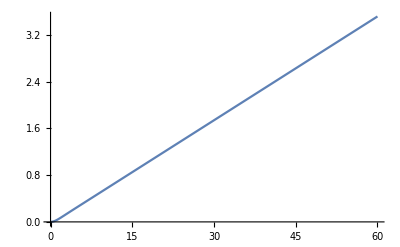
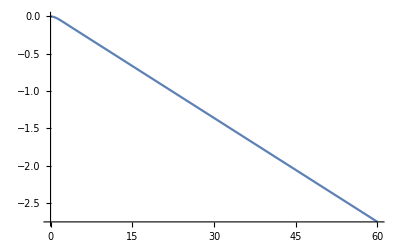
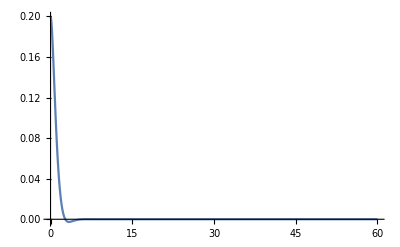
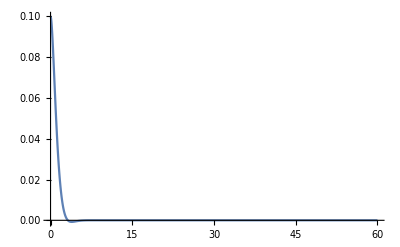
x[t] | z[t] | θ[t] | ϕ[t]
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{x[t],z[t],θ[t],ϕ[t]},Table[Plot[n,{t,0,60},PlotRange->Full],{n,sol}]}]
```

## Solve for x’’ and θ’’

```mathematica
textReplace=<|m1->Subscript[m, 1],m2->Subscript[m, 2],i->"I",Kpx->Subscript[P, x],Kdx->"D_x",Kpθ->Subscript[P, θ],Kdθ->"D_θ"|>
```

<|m1→m_1,m2→m_2,i→I,Kpx→P_x,Kdx→D_x,Kpθ→P_θ,Kdθ→D_θ|>

```mathematica
rules={x''[t]->xdd,θ''[t]->θdd, z''[t]->zdd, ϕ''[t]->ϕdd};
sol=Solve[eqs/.rules,{xdd,θdd, zdd, ϕdd}]/.(Reverse/@rules);
sol=Apply[Equal,#]&/@sol[[1]];
```

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification True⟦1⟧ is longer than depth of object.

```mathematica
Column[sol,Frame->All]//TraditionalForm
(*Export["eqn.svg",%]*)
```

Column[True⟦1⟧,Frame→All]

```mathematica
Symbol["I"]//TraditionalForm
```

ⅈ

```mathematica
sol/.textReplace
```

True⟦1⟧

## Linearize equations

```mathematica
motorPDRule=<|motor[t]->Kpx x[t]+Kpθ θ[t]+Kdx x'[t] +Kdθ θ'[t]|>
```

<|motor[t]→Kpx x[t]+Kpθ θ[t]+Kdx x'[t]+Kdθ θ'[t]|>

```mathematica
zeroMotorRule=<|Kpx->0 ,Kpθ ->0,Kdx ->0, Kdθ->0|>
```

<|Kpx→0,Kpθ→0,Kdx→0,Kdθ→0|>

```mathematica
linearizedEquations=MapAt[Simplify,Normal[Series[sol/.motorPDRule,{θ[t],0,1},{θ'[t],0,1},{x[t],0,1},{x'[t],0,1}]],{2,2}]
```

MapAt::partw: Part {2,2} of True⟦1⟧ does not exist.

MapAt[Simplify,True⟦1⟧,{2,2}]

```mathematica
linearizedEquations/.textReplace
```

MapAt[Simplify,True⟦1⟧,{2,2}]